```mathematica
With[
{tupleList = Subsets[Prime[Range[2,20]], {2,20}],
range=1000},
Monitor[
Table[
With[
{tuple=tupleList[[tuplePos]]},
With [{votes= DynamicVoteList[tuple,range]},

(*PrintTemporary[ToString[tuple] <> " ---> " <> ToString[tuplePos] <> " / " <> ToString[Length[tupleList]]];*)
{N[magicGraham[tuple]], N[Log[Last[votes] [[1]]   ]]}
]
]
, {tuplePos,1,Length[ tupleList]}
], ToString[tupleList[[tuplePos]]] <> " ---> "  <> ToString[tuplePos] <> " / " <> ToString[Length[tupleList]]
]
]
```

$Aborted

```mathematica
all=%
```

{{0.313536,16.4921},{0.343344,16.4811},{0.378151,13.4711},{0.389584,13.5599},{0.406454,13.2893},«8168»,{-1.79665,512.332},{-1.76184,497.928},{-1.73203,498.36},{-1.68035,491.06},{-2.04943,519.972}}

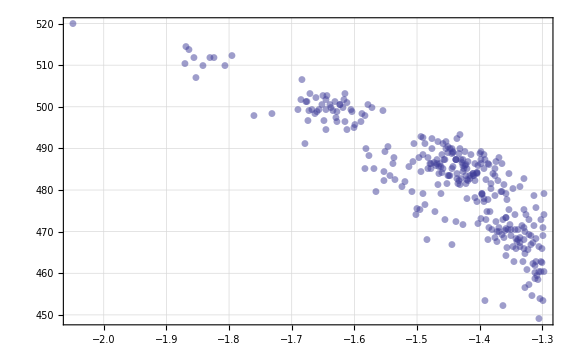

```mathematica
ListPlot[Sort[all], 
PlotMarkers->Automatic, 
AxesLabel->{"magic Graham for tuple", "Ln of nth value"},
AxesStyle->Directive[Thick, Darker[Darker[Green]],12],
AxesOrigin->{0,0},
PlotLabel->"Tuple magic value vs Ln of nth voted value\nFor 1000th voted value",
GridLines->Automatic,
Frame->True,
LabelStyle->{FontFamily->"Calibri", FontSize->Larger},
ImageSize->Large,
PlotRange->All,
PlotStyle->Opacity[0.5]
]
```